## Perturbation Documentation

## Preamble

```mathematica
Needs["Perturbation`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["Tensor`"]
Needs["Visualization`"]
```

## Introduction and Overview

This package provides a varied collection of tools which are commonly used to approximate and perturb quantum systems, although they can be used more generally. Mathematica’s ability to manipulate symbolic expressions is heavily exploited.

## Magnus Expansion

### MagnusExpansionTerm

MagnusExpansionTerm[{At,t,T},k] returns the k-th term in the magnus expansions (k=1,2,..) of the time dependent operator At with time parameter t, integrated over the time period 0 to T. This function is memoized.

Options
• Simplify→Identity (default) specifies that no intermittent simplifications are made during calculation.
• Simplify→True specifies that Simplify is called intermittently in the underlying function MagnusGenerator. This will often improve speed.
• Simplify→FullSimplify specifies that FullSimplify is called intermittently in the underlying function MagnusGenerator.

• Chop→True specifies that Chop is called intermittently in the underlying function MagnusGenerator.

#### Example

```mathematica
At=Sin[ω t]TP[X]+Cos[ω t]TP[Y];
MagnusExpansionTerm[{At,t,2π/ω},2,Simplify->True]//MatrixForm
```

((2 ⅈ π)/ω^2 | 0
0 | -(2 ⅈ π)/ω^2)

### MagnusExpansion

MagnusExpansion[{At,t,T},k] returns a list of the first k (k=1,2,3,..) terms of the Magnus expansion of time dependent operator At with time paramter t, intergrated over the period 0 to T.

Options
• Simplify→Identity (default) specifies that no intermittent simplifications are made during calculation.
• Simplify→True specifies that Simplify is called intermittently in the underlying function MagnusGenerator. This will often improve speed.
• Simplify→FullSimplify specifies that FullSimplify is called intermittently in the underlying function MagnusGenerator.

• Chop→True specifies that Chop is called intermittently in the underlying function MagnusGenerator.

#### Example

```mathematica
At=Sin[ω t]TP[X]+Cos[ω t]TP[Y];
MagnusExpansion[{At,t,2π/ω},3,Simplify->True]//MatrixListForm
```

(0 | 0
0 | 0),((2 ⅈ π)/ω^2 | 0
0 | -(2 ⅈ π)/ω^2),(0 | (4 ⅈ π)/ω^3
-(4 ⅈ π)/ω^3 | 0)

### MagnusGenerator

MagnusGenerator[{At,t,T},{n,j},fn] is the generator formula for the Magnus series; Ω_1=(∫_0)^T At(τ)dτ and Ω_n=∑_(j=1)^(n-1) S_n^j(τ)dτ for n>1, where Ω_n is the Magnus series, and S_n^j is MagnusGenerator. The generator formula was taken from Wikipedia’s article on the Magnus series. This function is memoized, and is used to computed Magnus terms for MagnusExpansionTerm and MagnusExpansion.

Options
• Simplify→Identity (default) specifies that no intermittent simplifications are made during calculation.
• Simplify→True specifies that Simplify is called intermittently. This will often improve speed.
• Simplify→FullSimplify specifies that FullSimplify is called intermittently.

• Chop→True specifies that Chop is called intermittently.

### MagnusConvergenceTest

MagnusConvergenceTest[{H,t,T}] performs the integral (∫_0)^T‖H(t)‖dt where ‖·‖ is the operator norm. If this quantity is less than π, then the Magnus series converges. This condition is sufficient but not necessary.

Options
• NIntegrate→True specifies that NIntegrate should be used rather than the default Integrate. Using Integrate will usually be very slow.

#### Analytic Example

```mathematica
At=Sin[ω t]TP[X]+Cos[ω t]TP[Y];
MagnusConvergenceTest[{At,t,2π/ω}]
```

ConditionalExpression[(2 √2 π)/ω,1/ω∈Reals]

#### Numeric Example

```mathematica
At=Sin[2.5 t]TP[X]+Cos[2.5 t]TP[Y];
MagnusConvergenceTest[{At,t,2π/2.5},NIntegrate->True]
2 √2 π/2.5
```

3.55431+0. ⅈ

3.55431

### References

The wikipedia article is correct and concise.

W. Magnus (1954). “On the exponential solution of differential equations for a linear operator”. Comm. Pure and Appl. Math. VII (4): 649–673.

## Average Hamiltonians

### AverageHamiltonianTerm

AverageHamiltonianTerm[{Ht,t,T},k] returns the k-th term in the average Hamiltonian expansion (k=0,1,2,..) of the time dependent Hamiltonian Ht with time parameter t, integrated over the time period 0 to T. This function is implemented by appropriately renormalizing the MagnusExpansionTerm function.

Options
• Simplify→Identity (default) specifies that no intermittent simplifications are made during calculation.
• Simplify→True specifies that Simplify is called intermittently in the underlying function MagnusGenerator. This will often improve speed.
• Simplify→FullSimplify specifies that FullSimplify is called intermittently in the underlying function MagnusGenerator.

• Chop→True specifies that Chop is called intermittently in the underlying function MagnusGenerator.

• NIntegrate→True specifies that NIntegrate should be used rather than the default Integrate.

#### Example

```mathematica
At=Sin[ω t]TP[X]+Cos[ω t]TP[Y];
AverageHamiltonianTerm[{At,t,2π/ω},1,Simplify->True]//MatrixForm
```

(1/ω | 0
0 | -1/ω)

### AverageHamiltonian

AverageHamiltonian[{Ht,t,T},k] returns the k-th average Hamiltonian (k=0,1,2,..) of the time dependent Hamiltonian Ht with time parameter t, integrated over the time period 0 to T. This function is equivalent to summing the results of AverageHamiltonianTerm from 0 to k.

Options
• Simplify→Identity (default) specifies that no intermittent simplifications are made during calculation.
• Simplify→True specifies that Simplify is called intermittently in the underlying function MagnusGenerator. This will often improve speed.
• Simplify→FullSimplify specifies that FullSimplify is called intermittently in the underlying function MagnusGenerator.

• Chop→True specifies that Chop is called intermittently in the underlying function MagnusGenerator.

• NIntegrate→True specifies that NIntegrate should be used rather than the default Integrate.

#### Example

```mathematica
At=Sin[ω t]TP[X]+Cos[ω t]TP[Y];
AverageHamiltonian[{At,t,2π/ω},2,Simplify->True]//MatrixForm
```

(1/ω | -(2 ⅈ)/ω^2
(2 ⅈ)/ω^2 | -1/ω)

### References

Haeberlen, U., Waugh, J.S., 1968. Coherent Averaging Effects in Magnetic Resonance. Phys. Rev. 175, 453–467. doi:10.1103/PhysRev.175.453

## Matrix Perturbations

### Eigenvectors

FirstOrderEigenvector[A,B,λ] performs first order perturbation theory on the eigenvectors corresponding to eigenvalue λ of A where B is the perturbation matrix. A does not have to be Hermitian, nor even Normal. λ can correspond to an eigenspace of dimension greater than 1. λ can also be a list of eigenvalues you want to perturb, or All, in which case perturbation theory is attempted on all eigenvaules.

Output is of the form {{v11,v12,...},{v21,v22,...},...} where v_(n,m) is the m^th degenerate eigenvector of the n^th eigenvalue.

#### Example

Define a simple A and B for which we don’t actually need perturbation theory.

```mathematica
A=TP[XI+IX];
B=ϵ TP[YI+IY];
```

Here are the eigenvalues:

```mathematica
Eigenvalues[A]
Eigenvalues[A+B]
```

{-2,2,0,0}

{0,0,-2 √(1+ϵ^2),2 √(1+ϵ^2)}

Let’s compute the corrected perturbative eigenvalues for the non-zero eigenvalues:

```mathematica
SecondOrderEigenvalue[A,B,{2,-2}]
```

{2+ϵ^2,-2-ϵ^2}

Note that this matches the Taylor expansion of the true eigenvalues:

```mathematica
Series[2 √(1+ϵ^2),{ϵ,0,2}]
```

2+ϵ^2+O[ϵ]^3

### Eigenvalues

SecondOrderEigenvalue[A,B,λ] performs second order perturbation theory on the eigenvalue λ of A where B is the perturbation matrix. A does not have to be Hermitian, nor even Normal. λ can correspond to an eigenspace of dimension greater than 1. λ can also be a list of eigenvalues you want to perturb, or All, in which case perturbation theory is attempted on all eigenvaules.

#### Example

Define a simple A and B for which we don’t actually need perturbation theory.

```mathematica
A=TP[XI+IX];
B=ϵ TP[YI+IY];
```

Let’s compute the corrections for the eigenvalue 2:

```mathematica
FirstOrderEigenvector[A,B,2]
```

{{{-ⅈ ϵ,0,0,ⅈ ϵ}}}

### References

Hinch, E.J., 1991. Perturbation Methods. Cambridge University Press.

## Zassenhaus Formula

### ZassenhausTerm

ZassenhausTerm[A,B,n] returns C_n (with n=0,1,2,...) from the Zassenhaus formula ⅇ^(t(A+B))=ⅇ^(t C_0)ⅇ^(t C_1)ⅇ^(t^2 C_2)ⅇ^(t^3 C_3)···  where A and B are square matrices. For example, C_0=A, C_1=B, C_2=-[A,B]/2, etc. This term is generated using ZassenhausGenerator. This function is memoized.

#### Example

```mathematica
A=TP[X];
B=TP[Y];
ZassenhausTerm[A,B,2]//MatrixForm
```

(-ⅈ | 0
0 | ⅈ)

As expected, this is equal to -[X,Y]/2:

```mathematica
-Com[A,B]/2//MatrixForm
```

(-ⅈ | 0
0 | ⅈ)

### ZassenhausSeries

ZassenhausSeries[A,B,n] returns the list {C_0,C_1,C_2,...,C_n} from the Zassenhaus formula ⅇ^(t(A+B))=ⅇ^(t C_0)ⅇ^(t C_1)ⅇ^(t^2 C_2)ⅇ^(t^3 C_3)···  where A and B are square matrices. For example, C_0=A, C_1=B, C_2=-[A,B]/2, etc. This these terms are generated using ZassenhausGenerator and ZassenhausTerm.

#### Example

```mathematica
A=TP[X];
B=TP[Y];
ZassenhausSeries[A,B,3]//MatrixListForm
```

(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(-ⅈ | 0
0 | ⅈ),(0 | -4/3-(2 ⅈ)/3
-4/3+(2 ⅈ)/3 | 0)

### ZassenhausExpansion

ZassenhausExpansion[t,A,B,n] calculates the right hand size of the Zassenhaus formula ⅇ^(t(A+B))=ⅇ^(t A)ⅇ^(t B)ⅇ^(-t^2[A,B]/2)···  to order ⅇ^(t^n). 
ZassenhausExpansion[A,B,n] calculates the right hand size of the Zassenhaus formula ⅇ^(t(A+B))=ⅇ^(t A)ⅇ^(t B)ⅇ^(-t^2[A,B]/2)···  to order ⅇ^(t^n) and then (effectively) sets t=1. 

This is done by first computing the Zassenhaus series using ZassenhausTerm and ZassenhausGenerator. See also ZassenhausSeries. This function is memoized.

#### Example

Compute orders 2 through 5 of the Zassenhaus expansion. Also compute the exact value.

```mathematica
A=-I TP[X];
B=-I TP[Y];
Table[ze[n]=ZassenhausExpansion[t,A,B,n],{n,2,5}];
ze[1]=MatrixExp[t(A+B)];
```

Plot the results.

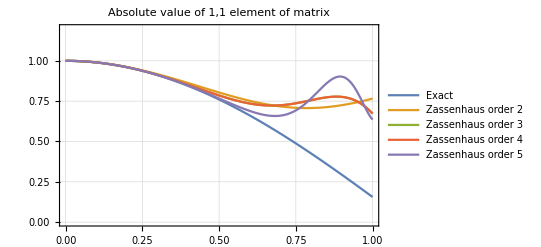

```mathematica
With[{functions=Table[Abs[ze[n]⟦1,1⟧],{n,1,5}]},
Plot[functions,{t,0,1},
PlotRange->{0,1.2},
PlotLegends->Prepend[Table["Zassenhaus order "<>ToString[n],{n,2,5}],"Exact"],
PlotLabel->"Absolute value of 1,1 element of matrix",
PlotTheme->"Detailed"
]
]
```

### ZassenhausGenerator

ZassenhausGenerator[X,Y,n,k] is the generator for the Zassenhaus expansion, implemented as ZassenhausExpansion. See attached reference in the documentation for more information. This function is memoized.

```mathematica
Com[TP[X],TP[Y],2]
```

{{0,-4 ⅈ},{4 ⅈ,0}}

### References

Casas, F., Murua, A., Nadinic, M., 2012. Efficient computation of the Zassenhaus formula. Computer Physics Communications 183, 2386–2391